```mathematica
x4p= Import["/Users/ashutosh/LCX_analysis/X1_4_T2_Mu_X_0.077"];
```

```mathematica
y4p= Import["/Users/ashutosh/LCX_analysis/X1_4_T2_Mu_Y_0.077"];
```

```mathematica
z4p= Import["/Users/ashutosh/LCX_analysis/X1_4_T2_Mu_Z_0.077"];
```

```mathematica
x4m= Import["/Users/ashutosh/LCX_analysis/X1_4_T2_Mu_X_-0.077"];
```

```mathematica
y4m= Import["/Users/ashutosh/LCX_analysis/X1_4_T2_Mu_Y_-0.077"];
```

```mathematica
z4m= Import["/Users/ashutosh/LCX_analysis/X1_4_T2_Mu_Z_-0.077"];
```

```mathematica
x19p= Import["/Users/ashutosh/LCX_analysis/X1_19_T2_Mu_X_0.077"];
```

```mathematica
y19p= Import["/Users/ashutosh/LCX_analysis/X1_19_T2_Mu_Y_0.077"];
```

```mathematica
z19p= Import["/Users/ashutosh/LCX_analysis/X1_19_T2_Mu_Z_0.077"];
```

```mathematica
x19m= Import["/Users/ashutosh/LCX_analysis/X1_19_T2_Mu_X_-0.077"];
```

```mathematica
y19m= Import["/Users/ashutosh/LCX_analysis/X1_19_T2_Mu_Y_-0.077"];
```

```mathematica
z19m= Import["/Users/ashutosh/LCX_analysis/X1_19_T2_Mu_Z_-0.077"];
```

```mathematica
MatrixPlot[x4p,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[z4p,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[z4m,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[x19p,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[x19m,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[y19p,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[y19m,PlotTheme->"Scientific"]
```

```mathematica
MatrixPlot[z19m,PlotTheme->"Scientific"]
```

```mathematica
diffxp = x19p - x4p;
```

```mathematica
f[i_,j_] := If[Abs[diffxp[[i,j]]]  > 0.005, diffxp[[i,j]] ,0 ]
```

```mathematica
my_mat = Array[f,{55,9}];
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0.0611463 | 0 | -0.0412902 | 0
0 | 0 | 0 | 0 | 0.00627846 | 0 | -0.0074675 | 0 | 0.134202
0 | 0 | 0 | 0 | 0 | 0 | 0.0079346 | 0 | 0.0870454
0 | 0 | 0 | 0 | 0 | 0.019694 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.00539221 | 0 | -0.011752 | 0 | 0.0708723
0 | 0 | 0 | 0 | 0.00522833 | 0 | -0.0104832 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0261395 | 0 | -0.0061048 | 0
0 | 0 | 0 | 0 | 0 | -0.0208507 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00641887 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0203718 | 0 | 0.012933 | 0 | 0.00941837
0 | 0 | 0 | 0 | 0 | -0.0312391 | 0 | 0.0231365 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.035222
0 | 0 | 0 | 0 | -0.00750168 | 0 | 0 | 0 | 0.0166117
0 | 0 | 0 | 0 | 0 | -0.00603736 | 0 | -0.0163303 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0241641
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0152831 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.01121 | 0 | 0.00853069 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0128118
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00819587 | 0
0 | 0 | 0 | 0 | 0.00531838 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00700273 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00958111
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0051894 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00662184
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
mymat = Table[f[i,j],{i,55},{j,9}];
```

```mathematica
mymat// MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0.0611463 | 0 | -0.0412902 | 0
0 | 0 | 0 | 0 | 0.00627846 | 0 | -0.0074675 | 0 | 0.134202
0 | 0 | 0 | 0 | 0 | 0 | 0.0079346 | 0 | 0.0870454
0 | 0 | 0 | 0 | 0 | 0.019694 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.00539221 | 0 | -0.011752 | 0 | 0.0708723
0 | 0 | 0 | 0 | 0.00522833 | 0 | -0.0104832 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0261395 | 0 | -0.0061048 | 0
0 | 0 | 0 | 0 | 0 | -0.0208507 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00641887 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0203718 | 0 | 0.012933 | 0 | 0.00941837
0 | 0 | 0 | 0 | 0 | -0.0312391 | 0 | 0.0231365 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.035222
0 | 0 | 0 | 0 | -0.00750168 | 0 | 0 | 0 | 0.0166117
0 | 0 | 0 | 0 | 0 | -0.00603736 | 0 | -0.0163303 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0241641
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0152831 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.01121 | 0 | 0.00853069 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0128118
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00819587 | 0
0 | 0 | 0 | 0 | 0.00531838 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00700273 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00958111
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0051894 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00662184
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
diffyp = y19p - y4p;
```

```mathematica
g[i_,j_] := If[Abs[diffxp[[i,j]]]  > 0.001, Abs[x19p[[i,j]]]-  Abs[x4p[[i,j]]],0 ];
```

```mathematica
diffxpmg = Table[g[i,j],{i,55},{j,9}];
```

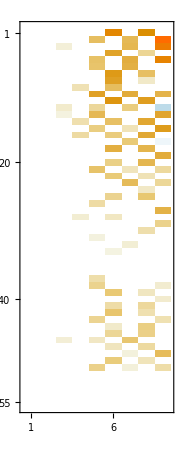

```mathematica
MatrixPlot[%243]
```

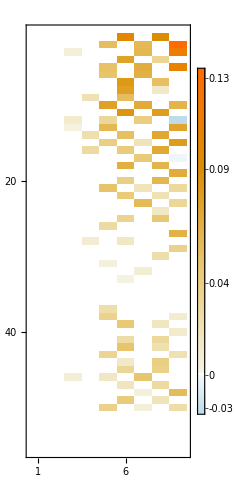

```mathematica
MatrixPlot[%243,PlotTheme->"Detailed"]
```

```mathematica
44.386877158174 - 42.263969908734
```

2.12291

```mathematica
42.57503685 -     39.935670605642
```

2.63937

```mathematica
42.5750368 - 31.742961063490
```

10.8321

```mathematica
44.386877158174 - 34.029644644730
```

10.3572

```mathematica
x0pcan= Import["/Users/ashutosh/LCX_analysis/can/X1_0_X1_Mu_X_0.077"];
filterss[i_,j_]:=If[Abs[ x0pcan[[i,j]]] > 0.05 ,x0pcan [[i,j]],0];
x0pcann = Table[filterss[i,j],{i,55},{j,9}];
```

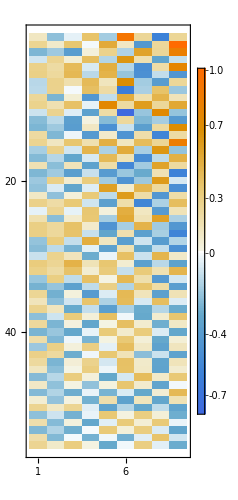

```mathematica
MatrixPlot[%683,PlotTheme->"Detailed"]
```

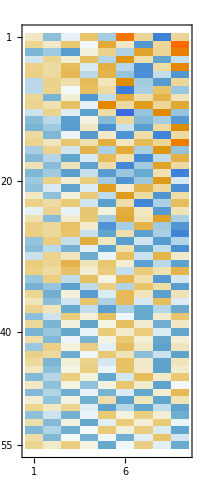

```mathematica
MatrixPlot[%301]
```

```mathematica
MatrixPlot[%301,PlotTheme->"Detailed"]
```

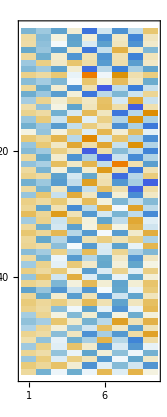
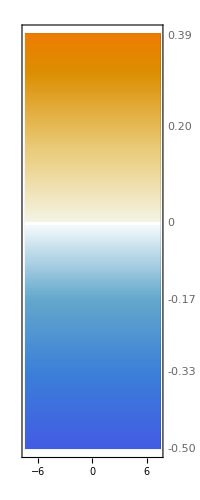
```mathematica
-Graphics- -Graphics--Graphics-
```

```mathematica
diffxp1 = x4p - x0pcan;
g1[i_,j_] := If[Abs[diffxp1[[i,j]]]  > 0.001, Abs[x4p[[i,j]]]-  Abs[x0pcan[[i,j]]],0 ];
diffxpmg1 = Table[g1[i,j],{i,55},{j,9}];
```

```mathematica
MatrixPlot[%296]
```

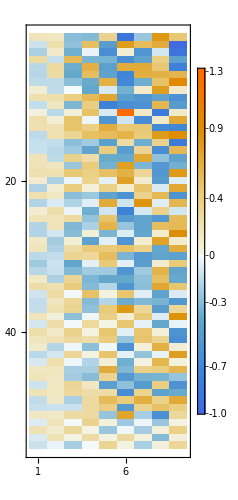

```mathematica
MatrixPlot[%296,PlotTheme->"Detailed"]
```

```mathematica
MatrixPlot[x4p]
```

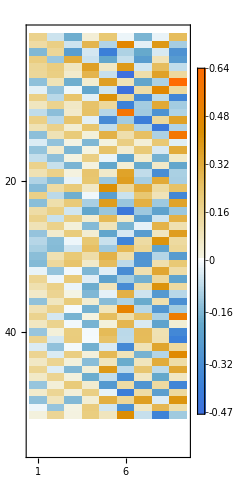

```mathematica
MatrixPlot[x4p,PlotTheme->"Detailed"]
```

```mathematica
MUX = Import["/Users/ashutosh/fno_expt/1.dat"];
```

```mathematica
MUiaXia = KroneckerProduct[MUX,x0pcan] //MatrixForm
```

```mathematica
g2[i_,j_] := MUX[[i,j]]*  x0pcan[[i,j]]
```

```mathematica
MUiaXia = Table[g2[i,j],{i,55},{j,9}];
```

```mathematica
MatrixPlot[%314]
```

```mathematica
MUiaXia //MatrixForm
```

```mathematica
MUX //MatrixForm
```

```mathematica
x0pcan //MatrixForm
```

(1.4838×10^-11 | -0.0000321199 | -2.727×10^-12 | 0.0147616 | -1.1874×10^-10 | 0.824601 | 3.03024×10^-10 | -0.374193 | 4.82251×10^-10
0.0000216366 | 9.997×10^-12 | 0.00812462 | -3.34×10^-13 | 0.136836 | 1.4102×10^-11 | -0.0816613 | 2.03857×10^-10 | 1.00784
-0.000301945 | -1.39553×10^-10 | -0.046555 | 2.472×10^-12 | 0.000150377 | -8.1023×10^-11 | 0.201263 | 2.57031×10^-10 | 0.652203
-1.4426×10^-11 | 0.0000313002 | 4.228×10^-12 | 0.0256354 | -6.7827×10^-11 | 0.312955 | 3.858×10^-11 | -0.0152239 | -2.9831×10^-11
0.000251906 | 1.16402×10^-10 | 0.0391634 | -8.58×10^-12 | 0.105705 | -6.3004×10^-11 | -0.197837 | 8.3095×10^-11 | 0.549791
0.000364373 | 1.68251×10^-10 | 0.0484351 | -5.2825×10^-11 | 0.0784499 | -3.25925×10^-10 | -0.181794 | -3.6413×10^-11 | -0.122364
-5.6214×10^-11 | 0.000122469 | 4.9344×10^-11 | 0.0407613 | 2.0528×10^-11 | 0.414737 | -1.23027×10^-10 | -0.0526079 | 2.16085×10^-10
-5.1482×10^-11 | 0.000111407 | -3.22×10^-13 | 0.023538 | 1.08329×10^-10 | -0.438129 | -9.9439×10^-11 | 0.0164712 | -1.78509×10^-10
2.07656×10^-10 | -0.000449318 | 3.954×10^-12 | -0.0985956 | -3.9209×10^-11 | 0.115834 | 5.0835×10^-11 | 0.0753904 | 3.0108×10^-11
0.0000886955 | 4.0985×10^-11 | 0.0195331 | -2.053×10^-12 | 0.5145 | 1.2543×10^-10 | 0.258348 | 2.15363×10^-10 | 0.152151
-2.2534×10^-11 | 0.0000486733 | -4.722×10^-12 | -0.0278193 | 1.0052×10^-10 | -0.792949 | -3.22545×10^-10 | 0.496133 | -4.20294×10^-10
-0.000114175 | -5.2768×10^-11 | -0.0296883 | 7.4×10^-13 | -0.000114271 | 1.88494×10^-10 | -0.000236686 | -1.14609×10^-10 | -0.0633786
-0.000317493 | -1.46712×10^-10 | -0.0435451 | 1.2414×10^-11 | -0.182562 | -2.5471×10^-11 | -0.0318053 | 1.37129×10^-10 | 0.416368
1.30778×10^-10 | -0.000283035 | -8.57×10^-13 | -0.0646061 | 9.899×10^-12 | -0.131505 | 6.3177×10^-11 | -0.330185 | 1.25131×10^-10
0.000034595 | 1.6101×10^-11 | 0.00930823 | 4.1138×10^-11 | 0.102879 | 1.8363×10^-11 | 0.0379517 | 3.55906×10^-10 | 0.689127
-1.0114×10^-10 | 0.000218778 | -1.0397×10^-11 | 0.0747322 | -8.4596×10^-11 | 0.133383 | -1.00287×10^-10 | 0.309142 | -4.67217×10^-10
-0.000134857 | -6.2347×10^-11 | -0.00922056 | -8.925×10^-12 | 0.0421581 | 3.2401×10^-11 | -0.217909 | -4.9868×10^-11 | 0.0941131
3.4884×10^-11 | -0.0000749435 | 3.0113×10^-11 | -0.0228682 | 7.6565×10^-11 | -0.297787 | -1.25117×10^-10 | 0.204495 | 1.33497×10^-10
-0.000291183 | -1.34667×10^-10 | -0.0342173 | -2.5992×10^-11 | -0.061207 | -1.9276×10^-10 | -0.00461569 | 3.3296×10^-11 | -0.372093
-1.46847×10^-10 | 0.000317657 | 6.231×10^-12 | 0.00238662 | -1.33567×10^-10 | -0.124771 | -1.55414×10^-10 | 0.272104 | -9.188×10^-12
-0.0000174453 | -7.881×10^-12 | -0.0138001 | -5.893×10^-12 | 0.230559 | 8.405×10^-12 | 0.063849 | 1.40785×10^-10 | -0.199114
1.1881×10^-11 | -0.0000255871 | 2.489×10^-12 | 0.00347275 | -4.715×10^-11 | 0.267235 | 8.2273×10^-11 | -0.102502 | 7.3358×10^-11
0.000186485 | 8.6101×10^-11 | 0.00531285 | -1.6097×10^-11 | -0.0278751 | 6.1704×10^-11 | -0.325111 | -8.6264×10^-11 | 0.0263921
-2.614×10^-12 | 5.57736×10^-6 | -2.494×10^-12 | 0.006902 | 2.1×10^-12 | 0.108693 | 1.5105×10^-11 | -0.0643534 | 3.0772×10^-11
4.4151×10^-11 | -0.0000950617 | 8.42×10^-12 | 0.0064438 | -1.15821×10^-10 | 0.149495 | 3.2064×10^-11 | 0.218136 | -9.7412×10^-11
0.000420255 | 1.94388×10^-10 | 0.0174695 | 9.639×10^-12 | -0.14265 | -1.0334×10^-10 | 0.0769053 | -1.34353×10^-10 | -0.100531
0.00041529 | 1.91608×10^-10 | 0.0155369 | -2.6523×10^-11 | -0.0133882 | 4.591×10^-11 | -0.029057 | -1.00519×10^-10 | -0.345037
-7.20961×10^-10 | 0.00155882 | -3.2956×10^-11 | 0.109126 | 1.7248×10^-11 | -0.0381539 | -1.6229×10^-11 | -0.0542996 | -6.8918×10^-11
-0.000108608 | -5.0226×10^-11 | -0.000744609 | -3.31×10^-12 | -0.0249608 | 3.5613×10^-11 | -0.010159 | -3.8686×10^-11 | -0.184326
-2.5357×10^-11 | 0.0000563499 | 2.5301×10^-11 | -0.00354894 | -1.204×10^-12 | 0.0220507 | -2.4151×10^-11 | 0.0731984 | 1.0746×10^-11
0.00216629 | 1.00175×10^-9 | 0.0820083 | 3.1075×10^-11 | 0.00779734 | 4.817×10^-12 | -0.0296084 | -5.3618×10^-11 | -0.0233564
0.00025416 | 1.17477×10^-10 | 0.0171068 | 4.63×10^-12 | 0.00275565 | -2.8584×10^-11 | 0.00284497 | 3.6315×10^-11 | 0.0719722
-2.72971×10^-10 | 0.000587665 | -4.0983×10^-11 | 0.021877 | 1.53×10^-13 | 0.0499956 | 5.3085×10^-11 | -0.0681818 | -1.0044×10^-11
-0.000803705 | -3.7272×10^-10 | -0.0236882 | -4.6508×10^-11 | 0.000402996 | -7.8836×10^-11 | 0.0103078 | 1.07819×10^-10 | -0.0350282
6.62467×10^-10 | -0.00143356 | 2.251×10^-12 | -0.0568434 | -6.123×10^-12 | 0.0468643 | 2.5765×10^-11 | -0.0287815 | 3.1397×10^-11
2.895×10^-11 | -0.0000624457 | -1.3509×10^-11 | 0.0134535 | -8.1697×10^-11 | 0.0403304 | -9.16×10^-12 | 0.0243702 | -5.933×10^-12
0.0000409636 | 1.9088×10^-11 | -0.00488665 | -3.088×10^-11 | -0.0305078 | -9.8702×10^-11 | -0.00388158 | -6.4095×10^-11 | -0.00379684
-0.0000373484 | -1.7156×10^-11 | 0.00265804 | 2.889×10^-12 | 0.0221452 | -5.65×10^-13 | -0.00536651 | 6.728×10^-12 | 0.00863718
1.82414×10^-10 | -0.000394607 | 1.626×10^-12 | -0.00790486 | 1.48×10^-13 | 0.0243418 | 4.88×10^-12 | -0.00294665 | 1.119×10^-11
-0.000485368 | -2.2429×10^-10 | -0.00734003 | -1.961×10^-12 | 0.00314916 | 9.217×10^-12 | 0.00259189 | -6.414×10^-12 | -0.00706035
7.3243×10^-11 | -0.000158511 | -7.54×10^-13 | -0.000587261 | 4.49×10^-13 | 0.00547406 | 3.411×10^-12 | -0.00625402 | 3.616×10^-12
-1.67298×10^-10 | 0.000362203 | 2.338×10^-12 | 0.000731259 | -3.196×10^-12 | 0.0270849 | 1.1829×10^-11 | -0.0193229 | 2.0453×10^-11
0.000304028 | 1.40205×10^-10 | -0.00312937 | -7.46×10^-13 | 0.00689551 | 3.0183×10^-11 | -0.0000946985 | -2.3368×10^-11 | -0.0171367
1.5221×10^-10 | -0.000330044 | 3.718×10^-12 | 0.000125118 | -9.67×10^-12 | 0.0199289 | 9.963×10^-12 | -0.01574 | 3.007×10^-11
1.8135×10^-11 | -0.0000392312 | 8.7×10^-14 | 0.00127221 | -8.75×10^-13 | 0.0178752 | 1.092×10^-11 | -0.0169817 | 7.38×10^-12
-0.000122526 | -5.6619×10^-11 | 0.00170567 | 2.448×10^-12 | -0.00638342 | -9.376×10^-12 | 0.0296094 | 1.0777×10^-11 | 0.00586511
1.1651×10^-11 | -0.0000251631 | 3.95×10^-13 | -0.0000193197 | 1.625×10^-12 | 0.00844371 | 7.511×10^-12 | -0.0145285 | -3.73×10^-13
-0.000153675 | -7.1069×10^-11 | -0.00311691 | -1.304×10^-12 | -0.000715587 | -7.771×10^-12 | -0.00632358 | 4.245×10^-12 | 0.0432477
4.781×10^-12 | -0.0000104584 | 6.44×10^-13 | -0.00160922 | 5.7522×10^-11 | -0.0231517 | 2.1434×10^-11 | -0.0102414 | 3.2288×10^-11
0.0000267774 | 1.2336×10^-11 | 7.0662×10^-6 | -4.693×10^-12 | -0.017577 | -6.7748×10^-11 | -0.00747096 | -4.1946×10^-11 | -0.0150012
-0.000037219 | -1.722×10^-11 | -0.00127346 | -1.409×10^-12 | 0.00609565 | 1.107×10^-12 | 0.00130518 | 3.334×10^-12 | -0.00307267
5.5318×10^-11 | -0.000119685 | 1.877×10^-12 | -0.00666708 | -4.229×10^-12 | 0.00294212 | 3.905×10^-12 | 0.00513476 | -9.95×10^-13
-0.000175076 | -8.0882×10^-11 | -0.00250691 | -5.6×10^-14 | 0.00461576 | 2.511×10^-12 | 0.00168807 | -7.073×10^-12 | -0.0102683
7.2668×10^-11 | -0.000157325 | -3.06×10^-13 | -0.00136011 | -5.93×10^-13 | -0.00226475 | -4.332×10^-12 | 0.0143177 | -1.1299×10^-11
0.0000218857 | 1.0145×10^-11 | 0.00150163 | 6.35×10^-13 | -0.00517679 | -4.87×10^-13 | 0.00103405 | -4.08×10^-12 | -0.00371299)

```mathematica
MUX = Import["/Users/ashutosh/fno_expt/full_MU_X","Table"]
```

{{2.106×10^-9,-0.00173864,9.×10^-12,-0.0189786,1.22×10^-10,-0.228302,-1.73×10^-10,0.0480283,-1.58×10^-10},{-0.00301463,-3.649×10^-9,-0.00891472,0.,-0.0759458,-5.3×10^-11,0.0238303,-1.04×10^-10,-0.140255},{0.00576403,6.975×10^-9,0.00695924,-2.1×10^-11,0.016874,9.3×10^-11,-0.101354,-1.77×10^-10,-0.0905749},{4.081×10^-9,-0.00337206,1.1×10^-11,-0.0201779,8.9×10^-11,-0.118248,-2.×10^-11,-0.0170527,-1.3×10^-11},{-0.00954382,-1.1548×10^-8,-0.0236382,2.8×10^-11,-0.0716514,3.×10^-12,0.082628,-3.×10^-12,-0.0887276},{-0.0102137,-1.2339×10^-8,-0.0198845,1.42×10^-10,-0.0605844,3.19×10^-10,0.0837912,1.55×10^-10,0.0566923},{7.738×10^-9,-0.0064209,-5.×10^-11,-0.0383448,-9.2×10^-11,-0.152632,2.23×10^-10,-0.0218319,5.4×10^-11},{1.499×10^-9,-0.00124072,-5.×10^-12,0.00315938,-1.71×10^-10,0.205956,8.5×10^-11,0.0205165,1.22×10^-10},{-1.4875×10^-8,0.0122935,-1.9×10^-11,0.0488687,5.×10^-11,-0.0316008,-4.3×10^-11,-0.0342006,1.×10^-12},{-0.00571881,-6.921×10^-9,-0.0341218,-1.×10^-12,-0.385812,-2.12×10^-10,-0.132426,-2.82×10^-10,-0.0408112},{5.84×10^-10,-0.000482128,-1.1×10^-11,0.0411932,-1.83×10^-10,0.481293,4.54×10^-10,-0.23511,5.29×10^-10},{0.00216865,2.624×10^-9,0.0106417,-2.3×10^-11,0.0292471,-2.5×10^-10,-0.0228305,1.67×10^-10,0.114562},{0.00861027,1.0418×10^-8,0.0363987,-3.×10^-11,0.156221,8.6×10^-11,0.0332162,-1.37×10^-10,-0.177528},{-1.1657×10^-8,0.00963325,-1.6×10^-11,0.0711403,-5.4×10^-11,0.10146,-1.16×10^-10,0.214062,-1.69×10^-10},{-0.00190024,-2.306×10^-9,-0.0211259,-6.6×10^-11,-0.0961743,2.×10^-11,-0.0310272,-5.03×10^-10,-0.387518},{1.0299×10^-8,-0.00850835,4.1×10^-11,-0.0795864,1.48×10^-10,-0.128574,1.62×10^-10,-0.212809,3.92×10^-10},{0.00449343,5.439×10^-9,0.029871,3.5×10^-11,-0.0637696,-1.02×10^-10,0.222668,1.27×10^-10,-0.0651027},{-6.823×10^-9,0.00561935,-9.6×10^-11,0.0393245,-2.19×10^-10,0.229027,1.99×10^-10,-0.127014,-1.21×10^-10},{0.0118754,1.4383×10^-8,0.0465458,8.4×10^-11,0.0866718,3.29×10^-10,0.0149463,1.5×10^-11,0.224863},{9.837×10^-9,-0.00812685,6.×10^-12,-0.0211608,4.91×10^-10,0.146422,4.66×10^-10,-0.311826,4.4×10^-11},{0.0000451702,4.3×10^-11,0.00390118,-7.×10^-12,-0.361241,-8.6×10^-11,-0.0658609,-3.94×10^-10,0.228504},{-1.615×10^-9,0.00133175,4.×10^-12,-0.025436,2.08×10^-10,-0.417831,-3.17×10^-10,0.141857,-2.71×10^-10},{-0.00555434,-6.716×10^-9,0.0406481,8.6×10^-11,0.028464,-2.63×10^-10,0.500034,3.52×10^-10,-0.00655708},{-6.97×10^-10,0.00057877,3.1×10^-11,-0.0141417,-1.8×10^-11,-0.189435,-4.1×10^-11,0.0895589,-1.27×10^-10},{-1.787×10^-9,0.00146301,-6.3×10^-11,-0.0516228,5.8×10^-10,-0.243029,-1.81×10^-10,-0.330958,3.91×10^-10},{-0.0126307,-1.5294×10^-8,-0.0468902,-1.×10^-12,0.285361,4.78×10^-10,-0.15822,5.33×10^-10,0.157464},{-0.00845043,-1.0202×10^-8,-0.00422463,1.45×10^-10,0.0163924,-1.65×10^-10,0.0627802,3.87×10^-10,0.471976},{4.9764×10^-8,-0.041092,2.04×10^-10,-0.190818,-6.2×10^-11,0.0224021,8.4×10^-11,0.0865816,2.71×10^-10},{0.00220789,2.676×10^-9,0.0214189,2.2×10^-11,0.0378575,-1.65×10^-10,0.0285194,1.86×10^-10,0.27486},{-2.604×10^-9,0.00212947,-9.9×10^-11,-0.00732172,1.7×10^-11,-0.0469927,5.9×10^-11,-0.115464,-8.1×10^-11},{-0.0551375,-6.6754×10^-8,-0.18475,-1.46×10^-10,-0.016828,1.2×10^-11,0.00271668,9.6×10^-11,-0.0290597},{-0.00946871,-1.146×10^-8,-0.042436,-2.×10^-11,-0.00265901,1.25×10^-10,0.00936149,-1.59×10^-10,-0.114911},{2.0309×10^-8,-0.0167049,2.8×10^-10,-0.0481103,1.9×10^-11,-0.0801927,-3.29×10^-10,0.141043,3.5×10^-11},{0.0211101,2.5635×10^-8,0.061897,2.67×10^-10,0.0064641,3.42×10^-10,-0.0341788,-6.1×10^-10,0.0583914},{-4.4642×10^-8,0.036893,-1.9×10^-11,0.128459,1.3×10^-11,-0.0590349,-1.1×10^-10,0.0631802,-1.15×10^-10},{-1.958×10^-9,0.00160541,1.09×10^-10,-0.0528885,5.47×10^-10,-0.0983908,-3.5×10^-11,-0.0588238,1.31×10^-10},{-0.00248756,-3.021×10^-9,0.0141504,3.25×10^-10,0.076813,6.42×10^-10,-0.00663906,4.04×10^-10,0.0231456},{0.00109709,1.321×10^-9,-0.0124742,-1.9×10^-11,-0.070126,-1.1×10^-11,0.0189498,-4.1×10^-11,-0.0142061},{-1.0849×10^-8,0.0089626,-1.7×10^-11,0.0146325,-1.5×10^-11,-0.0591235,-3.4×10^-11,0.0112973,-5.3×10^-11},{0.0156668,1.8954×10^-8,0.0418672,-2.×10^-12,0.00269502,-5.1×10^-11,0.00299153,2.6×10^-11,0.00170972},{-2.488×10^-9,0.00205845,8.×10^-12,0.00287094,-1.8×10^-11,0.00459058,-2.6×10^-11,0.0283679,-1.8×10^-11},{1.7308×10^-8,-0.0143089,-1.8×10^-11,-0.0335283,2.1×10^-11,-0.0570928,-6.×10^-11,0.0325966,-7.3×10^-11},{-0.00832224,-1.0054×10^-8,-0.00540777,4.4×10^-11,-0.0593463,-2.22×10^-10,0.0038338,2.5×10^-10,0.0683264},{-9.331×10^-9,0.00772885,1.×10^-11,0.0165148,1.64×10^-10,-0.0490849,-1.1×10^-10,0.0718552,-2.79×10^-10},{-2.459×10^-9,0.00203245,-1.×10^-12,-0.00146916,1.3×10^-11,-0.102964,-1.62×10^-10,0.0880865,-9.5×10^-11},{0.00196403,2.376×10^-9,-0.0242656,-4.7×10^-11,0.0388599,1.37×10^-10,-0.161246,-1.36×10^-10,-0.0207643},{1.43×10^-10,-0.00011803,0.,0.00329696,-3.7×10^-11,-0.0473715,-1.22×10^-10,0.0878892,-7.×10^-12},{0.000651167,7.89×10^-10,0.00173968,2.×10^-11,0.0128409,1.38×10^-10,0.0379373,-3.×10^-11,-0.181697},{8.69×10^-10,-0.000703268,-6.7×10^-11,0.0226009,-9.81×10^-10,0.147739,-3.13×10^-10,0.0554578,-6.1×10^-10},{-0.00229806,-2.787×10^-9,0.00779141,1.73×10^-10,0.112204,1.12×10^-9,0.0416232,6.04×10^-10,0.0968293},{0.00124193,1.504×10^-9,0.00112344,1.8×10^-11,-0.0313911,-1.8×10^-11,-0.0129414,-3.8×10^-11,0.0370861},{-3.163×10^-9,0.00261366,-2.5×10^-11,0.0392088,5.3×10^-11,-0.0119165,-2.4×10^-11,-0.03268,1.9×10^-11},{0.00538529,6.511×10^-9,0.0143464,0.,-0.0334991,-6.6×10^-11,-0.00671457,1.44×10^-10,0.0847944},{-9.321×10^-9,0.00770348,5.×10^-12,0.00860853,1.4×10^-11,0.0138539,8.4×10^-11,-0.0914821,1.86×10^-10},{-0.00380551,-4.61×10^-9,-0.00754825,-1.×10^-11,0.0339938,-1.×10^-12,0.00428501,8.1×10^-11,0.0238406}}

```mathematica
MUX //MatrixForm
```

(2.106×10^-9 | -0.00173864 | 9.×10^-12 | -0.0189786 | 1.22×10^-10 | -0.228302 | -1.73×10^-10 | 0.0480283 | -1.58×10^-10
-0.00301463 | -3.649×10^-9 | -0.00891472 | 0. | -0.0759458 | -5.3×10^-11 | 0.0238303 | -1.04×10^-10 | -0.140255
0.00576403 | 6.975×10^-9 | 0.00695924 | -2.1×10^-11 | 0.016874 | 9.3×10^-11 | -0.101354 | -1.77×10^-10 | -0.0905749
4.081×10^-9 | -0.00337206 | 1.1×10^-11 | -0.0201779 | 8.9×10^-11 | -0.118248 | -2.×10^-11 | -0.0170527 | -1.3×10^-11
-0.00954382 | -1.1548×10^-8 | -0.0236382 | 2.8×10^-11 | -0.0716514 | 3.×10^-12 | 0.082628 | -3.×10^-12 | -0.0887276
-0.0102137 | -1.2339×10^-8 | -0.0198845 | 1.42×10^-10 | -0.0605844 | 3.19×10^-10 | 0.0837912 | 1.55×10^-10 | 0.0566923
7.738×10^-9 | -0.0064209 | -5.×10^-11 | -0.0383448 | -9.2×10^-11 | -0.152632 | 2.23×10^-10 | -0.0218319 | 5.4×10^-11
1.499×10^-9 | -0.00124072 | -5.×10^-12 | 0.00315938 | -1.71×10^-10 | 0.205956 | 8.5×10^-11 | 0.0205165 | 1.22×10^-10
-1.4875×10^-8 | 0.0122935 | -1.9×10^-11 | 0.0488687 | 5.×10^-11 | -0.0316008 | -4.3×10^-11 | -0.0342006 | 1.×10^-12
-0.00571881 | -6.921×10^-9 | -0.0341218 | -1.×10^-12 | -0.385812 | -2.12×10^-10 | -0.132426 | -2.82×10^-10 | -0.0408112
5.84×10^-10 | -0.000482128 | -1.1×10^-11 | 0.0411932 | -1.83×10^-10 | 0.481293 | 4.54×10^-10 | -0.23511 | 5.29×10^-10
0.00216865 | 2.624×10^-9 | 0.0106417 | -2.3×10^-11 | 0.0292471 | -2.5×10^-10 | -0.0228305 | 1.67×10^-10 | 0.114562
0.00861027 | 1.0418×10^-8 | 0.0363987 | -3.×10^-11 | 0.156221 | 8.6×10^-11 | 0.0332162 | -1.37×10^-10 | -0.177528
-1.1657×10^-8 | 0.00963325 | -1.6×10^-11 | 0.0711403 | -5.4×10^-11 | 0.10146 | -1.16×10^-10 | 0.214062 | -1.69×10^-10
-0.00190024 | -2.306×10^-9 | -0.0211259 | -6.6×10^-11 | -0.0961743 | 2.×10^-11 | -0.0310272 | -5.03×10^-10 | -0.387518
1.0299×10^-8 | -0.00850835 | 4.1×10^-11 | -0.0795864 | 1.48×10^-10 | -0.128574 | 1.62×10^-10 | -0.212809 | 3.92×10^-10
0.00449343 | 5.439×10^-9 | 0.029871 | 3.5×10^-11 | -0.0637696 | -1.02×10^-10 | 0.222668 | 1.27×10^-10 | -0.0651027
-6.823×10^-9 | 0.00561935 | -9.6×10^-11 | 0.0393245 | -2.19×10^-10 | 0.229027 | 1.99×10^-10 | -0.127014 | -1.21×10^-10
0.0118754 | 1.4383×10^-8 | 0.0465458 | 8.4×10^-11 | 0.0866718 | 3.29×10^-10 | 0.0149463 | 1.5×10^-11 | 0.224863
9.837×10^-9 | -0.00812685 | 6.×10^-12 | -0.0211608 | 4.91×10^-10 | 0.146422 | 4.66×10^-10 | -0.311826 | 4.4×10^-11
0.0000451702 | 4.3×10^-11 | 0.00390118 | -7.×10^-12 | -0.361241 | -8.6×10^-11 | -0.0658609 | -3.94×10^-10 | 0.228504
-1.615×10^-9 | 0.00133175 | 4.×10^-12 | -0.025436 | 2.08×10^-10 | -0.417831 | -3.17×10^-10 | 0.141857 | -2.71×10^-10
-0.00555434 | -6.716×10^-9 | 0.0406481 | 8.6×10^-11 | 0.028464 | -2.63×10^-10 | 0.500034 | 3.52×10^-10 | -0.00655708
-6.97×10^-10 | 0.00057877 | 3.1×10^-11 | -0.0141417 | -1.8×10^-11 | -0.189435 | -4.1×10^-11 | 0.0895589 | -1.27×10^-10
-1.787×10^-9 | 0.00146301 | -6.3×10^-11 | -0.0516228 | 5.8×10^-10 | -0.243029 | -1.81×10^-10 | -0.330958 | 3.91×10^-10
-0.0126307 | -1.5294×10^-8 | -0.0468902 | -1.×10^-12 | 0.285361 | 4.78×10^-10 | -0.15822 | 5.33×10^-10 | 0.157464
-0.00845043 | -1.0202×10^-8 | -0.00422463 | 1.45×10^-10 | 0.0163924 | -1.65×10^-10 | 0.0627802 | 3.87×10^-10 | 0.471976
4.9764×10^-8 | -0.041092 | 2.04×10^-10 | -0.190818 | -6.2×10^-11 | 0.0224021 | 8.4×10^-11 | 0.0865816 | 2.71×10^-10
0.00220789 | 2.676×10^-9 | 0.0214189 | 2.2×10^-11 | 0.0378575 | -1.65×10^-10 | 0.0285194 | 1.86×10^-10 | 0.27486
-2.604×10^-9 | 0.00212947 | -9.9×10^-11 | -0.00732172 | 1.7×10^-11 | -0.0469927 | 5.9×10^-11 | -0.115464 | -8.1×10^-11
-0.0551375 | -6.6754×10^-8 | -0.18475 | -1.46×10^-10 | -0.016828 | 1.2×10^-11 | 0.00271668 | 9.6×10^-11 | -0.0290597
-0.00946871 | -1.146×10^-8 | -0.042436 | -2.×10^-11 | -0.00265901 | 1.25×10^-10 | 0.00936149 | -1.59×10^-10 | -0.114911
2.0309×10^-8 | -0.0167049 | 2.8×10^-10 | -0.0481103 | 1.9×10^-11 | -0.0801927 | -3.29×10^-10 | 0.141043 | 3.5×10^-11
0.0211101 | 2.5635×10^-8 | 0.061897 | 2.67×10^-10 | 0.0064641 | 3.42×10^-10 | -0.0341788 | -6.1×10^-10 | 0.0583914
-4.4642×10^-8 | 0.036893 | -1.9×10^-11 | 0.128459 | 1.3×10^-11 | -0.0590349 | -1.1×10^-10 | 0.0631802 | -1.15×10^-10
-1.958×10^-9 | 0.00160541 | 1.09×10^-10 | -0.0528885 | 5.47×10^-10 | -0.0983908 | -3.5×10^-11 | -0.0588238 | 1.31×10^-10
-0.00248756 | -3.021×10^-9 | 0.0141504 | 3.25×10^-10 | 0.076813 | 6.42×10^-10 | -0.00663906 | 4.04×10^-10 | 0.0231456
0.00109709 | 1.321×10^-9 | -0.0124742 | -1.9×10^-11 | -0.070126 | -1.1×10^-11 | 0.0189498 | -4.1×10^-11 | -0.0142061
-1.0849×10^-8 | 0.0089626 | -1.7×10^-11 | 0.0146325 | -1.5×10^-11 | -0.0591235 | -3.4×10^-11 | 0.0112973 | -5.3×10^-11
0.0156668 | 1.8954×10^-8 | 0.0418672 | -2.×10^-12 | 0.00269502 | -5.1×10^-11 | 0.00299153 | 2.6×10^-11 | 0.00170972
-2.488×10^-9 | 0.00205845 | 8.×10^-12 | 0.00287094 | -1.8×10^-11 | 0.00459058 | -2.6×10^-11 | 0.0283679 | -1.8×10^-11
1.7308×10^-8 | -0.0143089 | -1.8×10^-11 | -0.0335283 | 2.1×10^-11 | -0.0570928 | -6.×10^-11 | 0.0325966 | -7.3×10^-11
-0.00832224 | -1.0054×10^-8 | -0.00540777 | 4.4×10^-11 | -0.0593463 | -2.22×10^-10 | 0.0038338 | 2.5×10^-10 | 0.0683264
-9.331×10^-9 | 0.00772885 | 1.×10^-11 | 0.0165148 | 1.64×10^-10 | -0.0490849 | -1.1×10^-10 | 0.0718552 | -2.79×10^-10
-2.459×10^-9 | 0.00203245 | -1.×10^-12 | -0.00146916 | 1.3×10^-11 | -0.102964 | -1.62×10^-10 | 0.0880865 | -9.5×10^-11
0.00196403 | 2.376×10^-9 | -0.0242656 | -4.7×10^-11 | 0.0388599 | 1.37×10^-10 | -0.161246 | -1.36×10^-10 | -0.0207643
1.43×10^-10 | -0.00011803 | 0. | 0.00329696 | -3.7×10^-11 | -0.0473715 | -1.22×10^-10 | 0.0878892 | -7.×10^-12
0.000651167 | 7.89×10^-10 | 0.00173968 | 2.×10^-11 | 0.0128409 | 1.38×10^-10 | 0.0379373 | -3.×10^-11 | -0.181697
8.69×10^-10 | -0.000703268 | -6.7×10^-11 | 0.0226009 | -9.81×10^-10 | 0.147739 | -3.13×10^-10 | 0.0554578 | -6.1×10^-10
-0.00229806 | -2.787×10^-9 | 0.00779141 | 1.73×10^-10 | 0.112204 | 1.12×10^-9 | 0.0416232 | 6.04×10^-10 | 0.0968293
0.00124193 | 1.504×10^-9 | 0.00112344 | 1.8×10^-11 | -0.0313911 | -1.8×10^-11 | -0.0129414 | -3.8×10^-11 | 0.0370861
-3.163×10^-9 | 0.00261366 | -2.5×10^-11 | 0.0392088 | 5.3×10^-11 | -0.0119165 | -2.4×10^-11 | -0.03268 | 1.9×10^-11
0.00538529 | 6.511×10^-9 | 0.0143464 | 0. | -0.0334991 | -6.6×10^-11 | -0.00671457 | 1.44×10^-10 | 0.0847944
-9.321×10^-9 | 0.00770348 | 5.×10^-12 | 0.00860853 | 1.4×10^-11 | 0.0138539 | 8.4×10^-11 | -0.0914821 | 1.86×10^-10
-0.00380551 | -4.61×10^-9 | -0.00754825 | -1.×10^-11 | 0.0339938 | -1.×10^-12 | 0.00428501 | 8.1×10^-11 | 0.0238406)

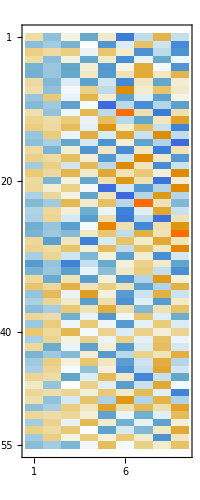

```mathematica
MatrixPlot[%335]
```

```mathematica
MUiaXia = Table[g2[i,j],{i,55},{j,9}];
```

```mathematica
MatrixPlot[%332,PlotTheme->"Detailed"]
```

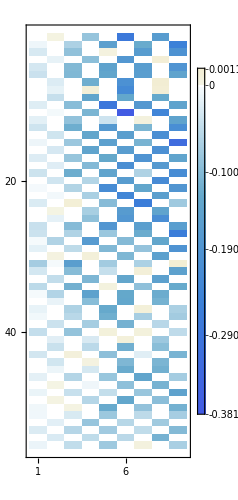
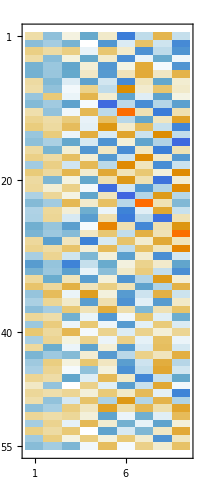
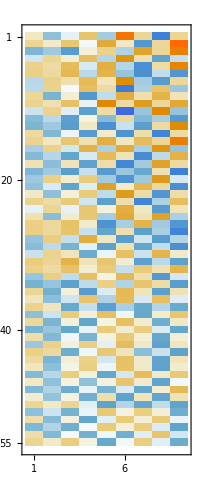

```mathematica
g2[i_,j_] := MUX[[i,j]]*  x4p[[i,j]];
```

```mathematica
MUiaXia4 =  Table[g2[i,j],{i,55},{j,9}];
```

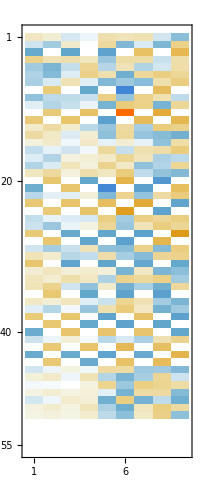

```mathematica
MatrixPlot[%339]
```